```mathematica
(*Числен анализ - курсов проект*)
(*Изготвил: Мартин Попов, 82134*)
```

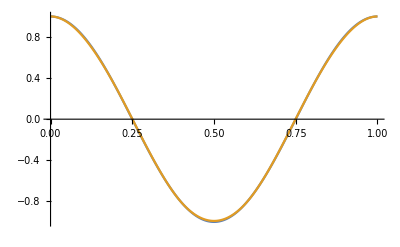

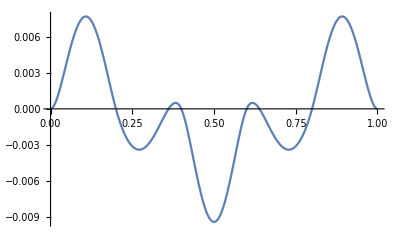

```mathematica
n=5;

(*функцията, която ще бъде интерполирана от търсения кубичен сплайн*)
f[t_]:=Cos[2*Pi*t];

(*инициализираме интерполационните възли*)
Do[x[k]=k/n,{k,0,n}];

(*разстоянието между всеки два съседни възела е константно*)
delta=1/n;

(*Запазваме функционалните стойности в променливи d[i]*)
Do[d[k]=f[x[k]],{k,0,n}];

(*Решаваме система по метода на прогонката*)
(*Изчисляваме коефициентите, които са константни, заради разстоянията*)
ca=1/delta;
cb=4/delta;
cc=1/delta;

(*смятаме стойностите от дясната страна на равенството*)
Do[values[k]=3*(d[k]-d[k-1])/delta^2+3*(d[k+1]-d[k])/delta^2,{k,1,n-1}];

(*намираме алфа и бета*)
alpha[1]=-cc/cb;
beta[1]=values[1]/cb;

(*намираме алфа[k] и бета[k] по правия ход на метода на прогонката*)
Do[alpha[k]=-cc/(ca*alpha[k-1]+cb),{k,2,n-2}];
Do[beta[k]=(values[k]-ca*beta[k-1])/(ca*alpha[k-1]+cb),{k,2,n-1}];

(*намираме c[0] и c[n] по следния начин, понеже имаме пълна кубична интерполация*)
c[0]=f'[x[0]];
c[n]=f'[x[n]];

(*задаваме c[n-1] по следния начин*)
c[n-1]=beta[n-1];

(*и пресмятаме останалите c[i] и останалите коефициенти a[i] и b[i] по обратния ход на метода на прогонката*)
For[k=n-2,k>0,k--,c[k]=alpha[k]*c[k+1]+beta[k]];
Do[a[k]=c[k+1]/delta^2+c[k]/delta^2+2*(d[k]-d[k+1])/delta^3,{k,0,n-1}];
Do[b[k]=(d[k+1]-d[k])/delta^2-c[k]/delta,{k,0,n-1}];

(*смятаме общия вид на полиномите, интерполиращи f(t) във всеки подинтервал на[0,1],определен от два последователни интерполационни възела*)
Do[p[k,z_]=a[k]*(z-x[k])^2*(z-x[k+1])+b[k]*(z-x[k])^2+c[k]*(z-x[k])+d[k],{k,0,n-1}];

(*рекурсивно построяваме кубичния сплайн за f(t), чрез интерполиращите полиноми за всеки един интервал*)
rec[i_,t_]:=If[i<=n+1,If[t>=x[i]&&t<x[i+1],p[i,t],rec[i+1,t]]];
spline[t_]:=rec[0,t];

(*чертаем графиките на нашата функция заедно със сплайн функцията*)
Plot[{f[t],spline[t]},{t,0,1},PlotPoints->300]

(*чертаем графиката на разликата на функцията и сплайн функцията*)
Plot[f[t]-spline[t],{t,0,1},PlotRange->All]
```